```mathematica
$HistoryLength=0;
figPath="/home/j/research/projects/prospectiveCoding/doc/pics/"(*NotebookDirectory[]*);
inCm[l_]:=Floor[(l 72)/2.54]
```

```mathematica
ps=Directive[AbsoluteThickness[1],#]&/@{waterColor=RGBColor[0,0,.5],goldColor=RGBColor[218/256,165/256,32/256]};inputColor=RGBColor[.6,.85,.6];inputColor2=RGBColor[0.0,0.5,0.0];
drawRect[c1_,c2_]:={inputColor,Rectangle[c1,c2]}
```

## Figure Rotation

```mathematica
t=2000; dt=1/10;n=20;
load[i_]:=
(post=Partition[Import[NotebookDirectory[]<>"../../data/rotationsPost"<>i<>".dat",{"Binary","Real64"}],5];
pre=Partition[Import[NotebookDirectory[]<>"../../data/rotationsPre"<>i<>".dat",{"Binary","Real64"}],2n];
)
load["_100"]
```

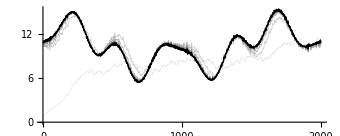

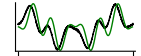

```mathematica
ListLinePlot[1000Partition[post[[All,1]],t/dt][[All,1;;-1;;10]],PlotRange->Automatic,ImageSize->inCm[12],LabelStyle->8,Axes->{True,True},AxesStyle->AbsoluteThickness[1],Ticks->{{0,{t/dt/10/2,t/2},{t/dt/10,t}},Automatic},AspectRatio->.4,ImagePadding->{{22,10},{All,All}},AxesOrigin->{0,0},PlotStyle->(Directive[GrayLevel[1-#/10],If[#==10,AbsoluteThickness[1],AbsoluteThickness[.5]]]&/@Range[10])]
figRotation=ListLinePlot[Standardize/@(5000 Partition[post[[All,#]],t/dt][[-1,1;;-1;;10]]&/@{1,4}),PlotRange->{{0,All},All},ImageSize->inCm[5],LabelStyle->8,Axes->{False,True},AxesStyle->AbsoluteThickness[1],Ticks->{{0,{t/dt/10/2,t/2},{t/dt/10,t}},None},AspectRatio->.4,ImagePadding->{{22,10},{All,All}},AxesOrigin->{0,-2.2},PlotStyle->{Directive[AbsoluteThickness[1],Black],Directive[AbsoluteThickness[1],inputColor2],Directive[Red]}]
```

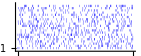

```mathematica
figRotationPre=Graphics[{AbsoluteThickness[.25],Blue,Line[{#+{0,-.5},#+{0,.5}}]}&/@Position[pre[[All,21;;-1]],1.],Axes->{True,True},AspectRatio->.4, ImageSize->inCm[5],ImagePadding->{{22,10},{All,All}},AxesStyle->AbsoluteThickness[1],LabelStyle->8,Ticks->{{0,{t/dt/2,t/2},{t/dt,t}},{1,20,100}},PlotRange->{{0,t/dt},{0,21}}]
```

```mathematica
corr[k_]:=Module[{s=post[[-3t/dt+k;;-t/dt+k,1]],t=post[[-3t/dt;;-t/dt,4]]},(s-Mean[s]).(t-Mean[t])]
acorr[k_]:=acorr[k,post[[-3t/dt;;-1,4]]]
acorr[k_,dat_]:=Module[{s=dat[[1+k;;t/dt+k]],t=dat[[1;;t/dt]]},(s-Mean[s]).(t-Mean[t])]
getMaxCC[i_]:=(
load["_"<>ToString[i]];
Position[#,Max@#]&@(corr/@Reverse@Range[4/5t/dt,t/dt-1])
)
```

```mathematica
getAlpha[τ_,τe_]:=1-τ/τe
range=Range[20,200,10];
```

```mathematica
resMaxCC002=Flatten[getMaxCC/@range dt]
```

{51/5,92/5,51/2,158/5,184/5,207/5,227/5,489/10,52,274/5,286/5,119/2,308/5,127/2,326/5,334/5,683/10,348/5,709/10}

```mathematica
{51/5,92/5,51/2,158/5,369/10,207/5,227/5,489/10,52,274/5,573/10,298/5,617/10,318/5,327/5,67,137/2,699/10,356/5}
```

```mathematica
getAlpha[9,100.]
```

0.91

```mathematica
figRotationCorrPeak=ListPlot[Transpose[{getAlpha[9,#]&/@range,resMaxCC002}],PlotStyle->Black,ImageSize->inCm[4],Ticks->{{.5,.75,1},{20,40,60}},AxesOrigin->{.3,0},PlotRange->{{.3,1},{0,75}},LabelStyle->8,AxesStyle->AbsoluteThickness[1],AspectRatio->.5,ImagePadding->{{18,8},{All,All}}]
```

-Graphics-

```mathematica
corrr[i_]:=(
load["_"<>ToString[i]];
corr/@Reverse@Range[t/dt 4/5,t/dt-1]
)
acorD=acorr/@Reverse@Range[t/dt 4/5,t/dt-1];
tPeak=First[Flatten@getMaxCC[100]];
cor=corrr/@{100};
tPeak dt//N
figRotationCorr=Show[ListLinePlot[{1,.7}(Standardize/@Append[cor,acorD]),PlotRange->{{0,200/dt},All},Ticks->{{#,#dt}&/@(1000Range[3]),None},AxesOrigin->{0,-1.6},AspectRatio->.5,PlotStyle->{Directive[AbsoluteThickness[1],Black],Directive[AbsoluteThickness[1],inputColor2]},LabelStyle->8,AxesStyle->AbsoluteThickness[1],ImageSize->inCm[4],ImagePadding->{{18,8},{All,All}}],Graphics[{Dashed,Line[{{tPeak,-1.6},{tPeak,1.6}}]}]]
```

52.

-Graphics-

```mathematica
figTauEff=Show[Sequence@@Table[Plot[τ/(1-α),{α,0,1},PlotRange->{{.68,1},{0,800}},AxesOrigin->{.68,0},Ticks->{Range[10]/10.,Range[0,1000,200]},LabelStyle->8,ImageSize->inCm[4],AspectRatio->1,AxesStyle->AbsoluteThickness[1],PlotStyle->(Directive[AbsoluteThickness[1],#]&/@{Black,Blue,RGBColor[0,.5,0],Red})[[τ/3-2]]],{τ,9,15,3}]]
```

-Graphics-

```mathematica
Export[figPath<>#<>".eps",ToExpression[#]]&/@{"figRotation", "figRotationPre","figRotationCorrPeak","figRotationCorr","figTauEff"}
```

{/home/j/research/projects/prospectiveCoding/src/mathematica/../../doc/pics/figRotation.eps,/home/j/research/projects/prospectiveCoding/src/mathematica/../../doc/pics/figRotationPre.eps,/home/j/research/projects/prospectiveCoding/src/mathematica/../../doc/pics/figRotationCorrPeak.eps,/home/j/research/projects/prospectiveCoding/src/mathematica/../../doc/pics/figRotationCorr.eps,/home/j/research/projects/prospectiveCoding/src/mathematica/../../doc/pics/figTauEff.eps}

## Figure Conditioning

```mathematica
dt = 1/10;n = 50;nw =2000;t=6000/dt;
tmp=Partition[Import[NotebookDirectory[]<>"../../data/conditioning.dat", {"Binary","Real64"}],4*n+12];
```

```mathematica
figCpre=ListLinePlot[(MovingAverage[#,200/dt]&/@Partition[tmp[[All,3n+#]],t]/dt 1000)[[All,1;;-1;;100]],PlotStyle->ps,PlotRange->All,ImageSize->inCm[4.5],DataRange->{0,4},Axes->{False,True},AxesStyle->AbsoluteThickness[1],ImagePadding->{{12,2},{10,2}},Ticks->{{1,2,3,4},{-10000,40}},LabelStyle->7,AspectRatio->.3]&@20
```

-Graphics-

```mathematica
figCSpikes=ArrayPlot[(Total/@Partition[#,10/dt])&/@Partition[tmp[[All,3n+20]],t][[2;;-1;;2]],AspectRatio->.2,ColorFunctionScaling->False,ColorFunction->(If[#≥1,goldColor,Transparent]&),ImagePadding->{{12,2},{0,0}},ImageSize->inCm[4.5],Frame->None]
```

-Graphics-

```mathematica
plot0[i_,o_,opt___]:=ListLinePlot[Partition[tmp[[All,-12+4(i-1)+o]],t][[All,1;;-1;;100]]/dt 1000,opt,PlotStyle->ps,PlotRange->All,ImageSize->inCm[4.5],AxesStyle->AbsoluteThickness[1],Ticks->{{t/dt/100/#,#-2}&/@Range[6],{20,40,60}},LabelStyle->8,AspectRatio->.4,ImagePadding->{{12,2},{10,2}}]
plot1[i_,o_,opt___]:=ListLinePlot[(Partition[tmp[[All,-12+4(i-1)+o]],t])[[All,1;;-1;;100]] 1000,opt,PlotStyle->ps,PlotRange->{{0,t/100},All},ImageSize->inCm[4.5],AxesStyle->AbsoluteThickness[1],Ticks->{{#t/100/6,#-1}&/@Range[6],{15,30,45}},LabelStyle->7,AspectRatio->.4,ImagePadding->{{12,2},{12,2}}]
plotP[i_,opt___]:=plot1[i,2,opt]
```

```mathematica
{figCBacon,figCWater}=plotP[#,Axes->{False,True}]&/@Range[2]
```

{-Graphics-,-Graphics-}

```mathematica
figCReward=plotP[3,AspectRatio->.42]
```

-Graphics-

```mathematica
Export[figPath<>#<>".eps",ToExpression[#]]&/@{"figCpre","figCBacon","figCWater","figCReward", "figCSpikes"}
```

{/home/j/research/projects/prospectiveCoding/doc/pics/figCpre.eps,/home/j/research/projects/prospectiveCoding/doc/pics/figCBacon.eps,/home/j/research/projects/prospectiveCoding/doc/pics/figCWater.eps,/home/j/research/projects/prospectiveCoding/doc/pics/figCReward.eps,/home/j/research/projects/prospectiveCoding/doc/pics/figCSpikes.eps}

## Figure RampUp

```mathematica
t=2000;n=20;dt=1/10;dx=10;
plotPost[dat_,startInput_:1800,xaxis_:True,i_:1]:=Show[Graphics[drawRect[{startInput/dx/dt,0},{t/dx/dt,60}]],ListLinePlot[1000 Partition[dat[[All,i]],t/dt][[All,1;;-1;;dx]],PlotRange->All,PlotStyle->(Directive[GrayLevel[1-#/10],If[#==10,AbsoluteThickness[1],AbsoluteThickness[.5]]]&/@Range[10])],PlotRange->All,ImageSize->inCm[4],LabelStyle->8,Axes->{xaxis,True},AxesStyle->AbsoluteThickness[1],Ticks->{{0,{t/dt/dx/2,t/2},{t/dt/dx,t}},{0,30,60}},AspectRatio->.4,ImagePadding->{{22,10},{All,All}}]
plotPre[dat_,showRate_:False]:=Show[If[showRate,ArrayPlot[Transpose[dat[[1;;-1;;10,20;;1;;-1]]],ColorFunction->(Blend[{White,Lighter[Blue,.7]},#]&),DataRange->{{1,t/dt},{1,20}}],Graphics[Rectangle[{0,0},{0,0}]]],Graphics[{AbsoluteThickness[.25],Blue,Line[{#+{0,-.5},#+{0,.5}}]}&/@Position[dat[[All,21;;-1]],1.]],Frame->{{True,False},{False,False}},PlotRangePadding->0, AspectRatio->.4, ImageSize->inCm[4],ImagePadding->{{22,10},{All,All}},FrameStyle->AbsoluteThickness[1],LabelStyle->8,FrameTicks->{None,{1,20}},PlotRange->{{0,t/dt},{0,21}},LabelStyle->8]
```

```mathematica
post=Partition[Import[NotebookDirectory[]<>"../../data/rampUpPost.dat",{"Binary","Real64"}],5];
pre=Partition[Import[NotebookDirectory[]<>"../../data/rampUpPre.dat",{"Binary","Real64"}],2];
postSpiking=Partition[Import[NotebookDirectory[]<>"../../data/rampUpSpikingPost.dat",{"Binary","Real64"}],5];
preSpiking=Partition[Import[NotebookDirectory[]<>"../../data/rampUpSpikingPre.dat",{"Binary","Real64"}],2 20];
postOU=Partition[Import[NotebookDirectory[]<>"../../data/predictOUPost.dat",{"Binary","Real64"}],5];
preOU=Partition[Import[NotebookDirectory[]<>"../../data/predictOUPre.dat",{"Binary","Real64"}],2 20];
postC=Partition[Import[NotebookDirectory[]<>"../../data/rampUpPostC.dat",{"Binary","Real64"}],5];
preC=Partition[Import[NotebookDirectory[]<>"../../data/rampUpPreC.dat",{"Binary","Real64"}],2];
postFP=Partition[Import[NotebookDirectory[]<>"../../data/rampUpFPPost.dat",{"Binary","Real64"}],5];
preFPLR=Partition[Import[NotebookDirectory[]<>"../../data/rampUpFPLRPre.dat",{"Binary","Real64"}],2 20];
postFPLR=Partition[Import[NotebookDirectory[]<>"../../data/rampUpFPLRPost.dat",{"Binary","Real64"}],5];
preFP=Partition[Import[NotebookDirectory[]<>"../../data/rampUpFPPre.dat",{"Binary","Real64"}],2 20];
postFPS=Partition[Import[NotebookDirectory[]<>"../../data/rampUpFPSPost.dat",{"Binary","Real64"}],5];
preFPS=Partition[Import[NotebookDirectory[]<>"../../data/rampUpFPSPre.dat",{"Binary","Real64"}],2 20];
postFPC=Partition[Import[NotebookDirectory[]<>"../../data/rampUpFPPostC.dat",{"Binary","Real64"}],5];
preFPC=Partition[Import[NotebookDirectory[]<>"../../data/rampUpFPPreC.dat",{"Binary","Real64"}],2];
postR=Partition[Import[NotebookDirectory[]<>"../../data/rampUpRatePost.dat",{"Binary","Real64"}],5];
preR=Partition[Import[NotebookDirectory[]<>"../../data/rampUpRatePre.dat",{"Binary","Real64"}],2 20];
postROU=Partition[Import[NotebookDirectory[]<>"../../data/rampUpRateOUPost.dat",{"Binary","Real64"}],5];
preROU=Partition[Import[NotebookDirectory[]<>"../../data/rampUpRateOUPre.dat",{"Binary","Real64"}],2 20];
postRC=Partition[Import[NotebookDirectory[]<>"../../data/rampUpRatePostC.dat",{"Binary","Real64"}],5];
preRC=Partition[Import[NotebookDirectory[]<>"../../data/rampUpRatePreC.dat",{"Binary","Real64"}],1600];
```

Import::nffil: File not found during Import.

Partition::pdep: Depth 1 requested in object with dimensions {}.

Import::nffil: File not found during Import.

Partition::pdep: Depth 1 requested in object with dimensions {}.

Import::nffil: File not found during Import.

Partition::pdep: Depth 1 requested in object with dimensions {}.

Import::nffil: File not found during Import.

Partition::pdep: Depth 1 requested in object with dimensions {}.

Import::nffil: File not found during Import.

Partition::pdep: Depth 1 requested in object with dimensions {}.

Import::nffil: File not found during Import.

Partition::pdep: Depth 1 requested in object with dimensions {}.

Import::nffil: File not found during Import.

Partition::pdep: Depth 1 requested in object with dimensions {}.

Import::nffil: File not found during Import.

Partition::pdep: Depth 1 requested in object with dimensions {}.

Import::nffil: File not found during Import.

Partition::pdep: Depth 1 requested in object with dimensions {}.

Import::nffil: File not found during Import.

Partition::pdep: Depth 1 requested in object with dimensions {}.

```mathematica
figEpsp=ListPlot[RandomSample[Mod[Range[0,1t/dt-dt],t/dt][[1;;-1;;100]]],PlotStyle->Directive[AbsoluteThickness[1],Blue],PlotMarkers ->Graphics[{AbsoluteThickness[.5],Blue,Line[{{0,-.005},{0,.005}}]}],ImageSize->inCm[4],LabelStyle->8,AspectRatio->.45,ImagePadding->{{22,6},{All,All}},Axes->{False,True},AxesStyle->AbsoluteThickness[1],Ticks->{None,{{t/dt/2,t/2},{t/dt,t}}},AxesOrigin->{0,0}]
```

-Graphics-

```mathematica
figDWD=ListLinePlot[(#/Max@#)&/@{pre[[1;;400,1]],pre[[1;;400,2]]},ImageSize->inCm[1.6],LabelStyle->8,PlotRange->All,AxesStyle->AbsoluteThickness[1],Ticks->{{0,{200,20},{400,40}},None},PlotStyle->{Directive[AbsoluteThickness[1.5],Blue,Dashed],Directive[AbsoluteThickness[1],RGBColor[1,0,0,.5]]}]
```

-Graphics-

```mathematica
figDWS=ListLinePlot[{preC[[1;;400,1]],preC[[1;;400,2]]},ImageSize->inCm[1.6],LabelStyle->8,PlotRange->All,AxesStyle->AbsoluteThickness[1],Ticks->None,PlotStyle->{Directive[AbsoluteThickness[1.5],Blue,Dashed],Directive[AbsoluteThickness[1],RGBColor[1,0,0,.5]]}]
```

-Graphics-

```mathematica
getTheory[gEatUS_]:=Module[{gE, Us, phiUs, α,gamma},
gE=Table[If[t>1800/dt,gEatUS,0],{t,2000/dt}];
Us=gE 14/3/(1800+100+gE);
phiUs = 60 Us;
α = 1-Exp[-dt/10+dt/600.];
gamma = Table[Exp[-dt t/600.],{t,0,4000/dt}];
ListConvolve[Reverse[gamma],phiUs,1]/(10/dt)
]
theory=getTheory[15];
theory2=getTheory[7.5];
```

```mathematica
figD1=Show[plotPost[post],ListLinePlot[theory[[1;;-1;;1/dt]],PlotStyle->Directive[AbsoluteThickness[1],Red,Dashed]]]
```

-Graphics-

```mathematica
figFPPre=plotPre[preFP,False]
```

-Graphics-

```mathematica
figD2=Show[plotPost[postFP],ListLinePlot[theory[[1;;-1;;1/dt]],PlotStyle->Directive[AbsoluteThickness[1],Red,Dashed]]]
```

-Graphics-

```mathematica
figD2OU=Show[plotPost[postROU],ListLinePlot[theory[[1;;-1;;1/dt]],PlotStyle->Directive[AbsoluteThickness[1],Red,Dashed]]]
```

-Graphics-

```mathematica
figD2OUPre=plotPre[preROU,True]
```

-Graphics-

```mathematica
figFPSPre=plotPre[preFPS,True]
figD2S=Show[plotPost[postFPS],ListLinePlot[theory2[[1;;-1;;1/dt]],PlotStyle->Directive[AbsoluteThickness[1],Red,Dashed]]]
```

-Graphics-

-Graphics-

```mathematica
figS1=plotPost[postC,1800,False]
```

-Graphics-

```mathematica
figS2=plotPost[postFPC,1800,False]
```

-Graphics-

```mathematica
figThreeStimPre=plotPre[preR,True]
```

-Graphics-

```mathematica
figThreeStimPost=plotPost[postR,2t/3]
```

-Graphics-

```mathematica
figThreeStimPostC=plotPost[postRC,2t/3,False]
```

-Graphics-

```mathematica
Export[figPath<>#<>".eps",ToExpression[#]]&/@{"figEpsp","figDWD","figDWS","figD1","figS1","figD2","figS2","figFPPre","figFPSPre","figNudge","figThreeStimPost","figThreeStimPostC", "figThreeStimNudge","figThreeStimPre","figD2S","figD2OU","figD2OUPre"}
```

{/home/j/research/projects/prospectiveCoding/src/mathematica/../../doc/pics/figEpsp.eps,/home/j/research/projects/prospectiveCoding/src/mathematica/../../doc/pics/figDWD.eps,/home/j/research/projects/prospectiveCoding/src/mathematica/../../doc/pics/figDWS.eps,/home/j/research/projects/prospectiveCoding/src/mathematica/../../doc/pics/figD1.eps,/home/j/research/projects/prospectiveCoding/src/mathematica/../../doc/pics/figS1.eps,/home/j/research/projects/prospectiveCoding/src/mathematica/../../doc/pics/figD2.eps,/home/j/research/projects/prospectiveCoding/src/mathematica/../../doc/pics/figS2.eps,/home/j/research/projects/prospectiveCoding/src/mathematica/../../doc/pics/figFPPre.eps,/home/j/research/projects/prospectiveCoding/src/mathematica/../../doc/pics/figFPSPre.eps,/home/j/research/projects/prospectiveCoding/src/mathematica/../../doc/pics/figNudge.eps,/home/j/research/projects/prospectiveCoding/src/mathematica/../../doc/pics/figThreeStimPost.eps,/home/j/research/projects/prospectiveCoding/src/mathematica/../../doc/pics/figThreeStimPostC.eps,/home/j/research/projects/prospectiveCoding/src/mathematica/../../doc/pics/figThreeStimNudge.eps,/home/j/research/projects/prospectiveCoding/src/mathematica/../../doc/pics/figThreeStimPre.eps,/home/j/research/projects/prospectiveCoding/src/mathematica/../../doc/pics/figD2S.eps,/home/j/research/projects/prospectiveCoding/src/mathematica/../../doc/pics/figD2OU.eps,/home/j/research/projects/prospectiveCoding/src/mathematica/../../doc/pics/figD2OUPre.eps}

## Figure Recurrent

```mathematica
dt = 1/10;n = 200;t=40/dt;
dir="/home/j/research/projects/prospectiveCoding/data/";
tmp=Partition[Import[dir<>"planning.dat", {"Binary","Real64"}],2n];
wd = Import[dir<>"planningWD.dat", {"Binary","Real64"}];
ww = Import[dir<>"planningW.dat", {"Binary","Real64"}];
```

```mathematica
www=Partition[ww,n];
MatrixPlot[www,Frame->None,FrameStyle->AbsoluteThickness[1],ImageSize->inCm[2.5],FrameTicks->None]
```

-Graphics-

```mathematica
Length@tmp
```

32000

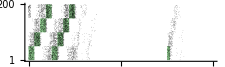

```mathematica
figRec=Graphics[Join[Append[{drawRect[{#,Mod[#,4]}{1000,n/4},{#+1,Mod[#,4]+1}{1000,n/4}]&/@Range[0,7]},drawRect[{6 4000,0},{6 4000+1 4000/8,50}]],{AbsoluteThickness[.25],Black,Line[{#+{0,-.5},#+{0,.5}}]}&/@Position[tmp[[1;;-1,1;;n]],1.]],Axes->{True,True},AspectRatio->.3, ImageSize->inCm[8],ImagePadding->{{22,10},{All,All}},AxesStyle->AbsoluteThickness[1],LabelStyle->8,Ticks->{({#,#dt}&/@Range[0,Length@tmp,Length@tmp/4]),{1,100,200}},PlotRange->{{0,Length@tmp},{0,200}}]
```

```mathematica
Export[figPath<>"doc/pics/"<>#<>".eps",ToExpression[#]]&/@{"figRec"}
```

{/home/j/research/projects/prospectiveCoding/doc/pics/figRec.eps}